```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
αcont={0.5135036591175975,0.0023893085927788557}; 
σcont={0.16963079795754127,0.00084757894486039};
ccont={-0.15964102962645102,0.0023730768366581885};
```

```mathematica
Πpar[θ_,u_,mD_]:=mD^2/2((2-2 u^2-u^4 Cos[θ]^2 Sin[θ]^2)/((1-u^2 Sin[θ]^2)^2)-((2+u^2 Sin[θ]^2)(1-u^2)u Cos[θ])/(2(1-u^2 Sin[θ]^2)^(5/2))Log[(u Cos[θ]+√(1-u^2 Sin[θ]^2))/(u Cos[θ]-√(1-u^2 Sin[θ]^2))])
```

```mathematica
ϵp[p_,mD_,T_]:=p^2/(p^2+mD^2)-ⅈ π T(p mD^2)/((p^2+mD^2)^2);
```

```mathematica
ϵu0[r_,mD_,T_]:=-(ⅇ^(-mD r) mD^2)/(4π r)-ⅈ T(mD √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(mD^2 r^2)/4])/(4 π r);
```

## Real part

```mathematica
ϵRe[r_,u_,mD_]:=1/(4π) NIntegrate[Sin[θ] Re[Πpar[θ,u,mD]]^(3/2)Exp[-√Re[Πpar[θ,u,mD]]r Cos[θ]],{θ,0,π/2}];
```

```mathematica
ReVcp[r_,mD_,u_,α_]:=-α/r+α NIntegrate[Sin[θ] √Re[Πpar[θ,u,mD]] Exp[-√Re[Πpar[θ,u,mD]]r Cos[θ]],{θ,0,π/2}];
```

```mathematica
ϵRep[r_,u_,mD_]:=1/(4π)(2/r NIntegrate[Cos[θ]Sin[θ]Re[Πpar[θ,u,mD]]Exp[-√Re[Πpar[θ,u,mD]]r Cos[θ]],{θ,0,π/2}]-NIntegrate[Cos[θ]^2 Sin[θ] Re[Πpar[θ,u,mD]]^(3/2)Exp[-√Re[Πpar[θ,u,mD]]r Cos[θ]],{θ,0,π/2}]);
```

```mathematica
(*check limit for u->0*)
```

```mathematica
1/(4π) Integrate[Sin[x] mD^3 Exp[-mD r Cos[x]],{x,0,π/2}](*ϵRe*)
```

((1-ⅇ^(-mD r)) mD^2)/(4 π r)

```mathematica
1/(4π)(2/r Integrate[Cos[θ]Sin[θ]mD Exp[-mD r Cos[θ]],{θ,0,π/2}]-Integrate[Cos[θ]^2 Sin[θ] mD^3 Exp[-mD r Cos[θ]],{θ,0,π/2}])//FullSimplify(*ϵRep*)
```

(ⅇ^(-mD r) (-2-2 ⅇ^(mD r) (-1+mD)+mD (2+r (-2+mD (2+mD r)))))/(4 mD π r^3)

```mathematica
(*permittivity from paper gives numerically correct result for u->0*)
```

```mathematica
ϵRep[2/0.197,0,0.2]
```

0.0000411595

```mathematica
N[ϵu0[2/0.197,0.2,0]]
```

-0.0000411595

```mathematica
(*note that adding a term ~1/r fixes the Fourier transform version*)
```

```mathematica
1/(4π) Integrate[Sin[x] mD^3 Exp[-mD r Cos[x]],{x,0,π/2}]-mD^2/(4π r)//FullSimplify(*ϵRe with additional term as u->0*)
```

-(ⅇ^(-mD r) mD^2)/(4 π r)

## Imaginary part

```mathematica
ϵImM[r_,mD_,u_,T_]:=(mD^2 T)/(4π)NIntegrate[((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))Sin[x]/(2 (Πpar[x,u,mD]-Conjugate[Πpar[x,u,mD]]))ⅈ (ⅈ Πpar[x,u,mD] √π MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 Πpar[x,u,mD] r^2 Cos[x]^2]+Πpar[x,u,mD] π Sign[r Cos[x]] (Cosh[√Πpar[x,u,mD] Abs[r] Abs[Cos[x]]]-Sinh[√Πpar[x,u,mD] Abs[r] Abs[Cos[x]]])+Conjugate[Πpar[x,u,mD]] (-ⅈ √π MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 Conjugate[Πpar[x,u,mD]] Cos[x]^2]+π Sign[r Cos[x]] (-Cosh[Abs[r] Abs[Cos[x]] √Conjugate[Πpar[x,u,mD]]]+Sinh[Abs[r] Abs[Cos[x]] √Conjugate[Πpar[x,u,mD]]]))),{x,0,π}];(*mathematica version*)
```

```mathematica
ImVcp[r_,mD_,u_,α_,T_]:=-2 α T NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))mD^2/(Πpar[x,u,mD]-Conjugate[Πpar[x,u,mD]])(Sinh[√Πpar[x,u,mD] r Cos[x]]SinhIntegral[√Πpar[x,u,mD] r Cos[x]]-Cosh[√Πpar[x,u,mD] r Cos[x]]CoshIntegral[√Πpar[x,u,mD] r Cos[x]]-Sinh[√Conjugate[Πpar[x,u,mD]] r Cos[x]]SinhIntegral[√Conjugate[Πpar[x,u,mD]] r Cos[x]]+Cosh[√Conjugate[Πpar[x,u,mD]] r Cos[x]]CoshIntegral[√Conjugate[Πpar[x,u,mD]] r Cos[x]]),{x,0,π/2}];
```

```mathematica
ϵImp[r_,mD_,u_,T_]:=Re[1/(2π)T NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))mD^2/(Πpar[x,u,mD]-Conjugate[Πpar[x,u,mD]])1/r Cos[x] (2 √Conjugate[Πpar[x,u,mD]] (CoshIntegral[r √Conjugate[Πpar[x,u,mD]] Cos[x]] Sinh[r √Conjugate[Πpar[x,u,mD]] Cos[x]]-Cosh[r √Conjugate[Πpar[x,u,mD]] Cos[x]] SinhIntegral[r √Conjugate[Πpar[x,u,mD]] Cos[x]])+r Conjugate[Πpar[x,u,mD]] Cos[x] (Cosh[r √Conjugate[Πpar[x,u,mD]] Cos[x]] CoshIntegral[r √Conjugate[Πpar[x,u,mD]] Cos[x]]-Sinh[r √Conjugate[Πpar[x,u,mD]] Cos[x]] SinhIntegral[r √Conjugate[Πpar[x,u,mD]] Cos[x]])+√Πpar[x,u,mD] (-CoshIntegral[r Cos[x] √Πpar[x,u,mD]] (r Cos[x] Cosh[r Cos[x] √Πpar[x,u,mD]] √Πpar[x,u,mD]+2 Sinh[r Cos[x] √Πpar[x,u,mD]])+(2 Cosh[r Cos[x] √Πpar[x,u,mD]]+r Cos[x] √Πpar[x,u,mD] Sinh[r Cos[x] √Πpar[x,u,mD]]) SinhIntegral[r Cos[x] √Πpar[x,u,mD]])),{x,0,π/2}]];
```

```mathematica
(*check limit for u->0*)
```

```mathematica
ϵImM[2/(197/1000),2/10,10^-10,155/1000]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.60463834122208}. NIntegrate obtained -0.0300968+0.000754429 ⅈ and 0.000529302 for the integral and error estimates.

-0.0000148492+3.72221×10^-7 ⅈ

```mathematica
ϵImp[2/(197/1000),2/10,10^-10,155/1000]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.662655}. NIntegrate obtained 0.00195438-1.21687×10^-8 ⅈ and 2.16584×10^-8 for the integral and error estimates.

0.0000482125

```mathematica
N[Im[ϵu0[2/(197/1000),2/10,155/1000]]]
```

-0.0000482128

```mathematica
(*compare results*)
```

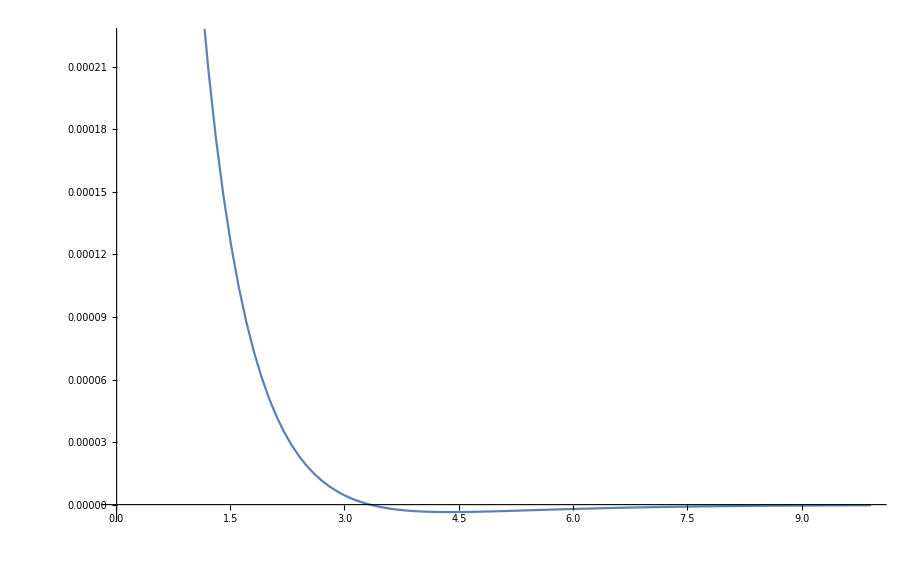

```mathematica
Quiet[DiscretePlot[Re[ϵImM[r/(197/1000),2/10,2/10,155/1000]],{r,1/100,10,1/10},Filling->None,Joined->True]]
```

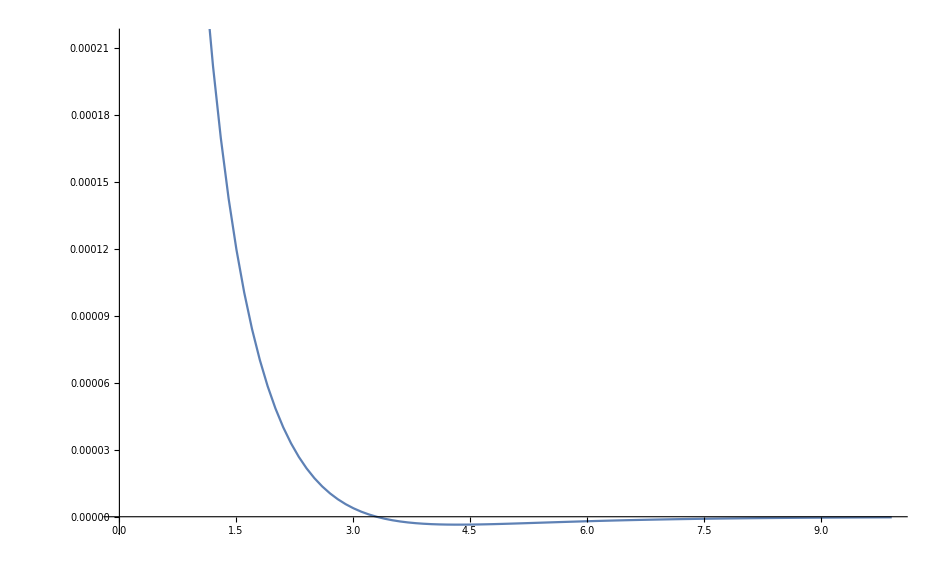

```mathematica
Quiet[DiscretePlot[Re[ϵImp[r/(197/1000),2/10,2/10,155/1000]],{r,1/100,10,1/10},Filling->None,Joined->True]]
```

## Potentials

### String

```mathematica
ϵRep[r_,u_,mD_]:=1/(4π)(2/r NIntegrate[Cos[θ]Sin[θ]Re[Πpar[θ,u,mD]]Exp[-√Re[Πpar[θ,u,mD]]r Cos[θ]],{θ,0,π/2}]-NIntegrate[Cos[θ]^2 Sin[θ] Re[Πpar[θ,u,mD]]^(3/2)Exp[-√Re[Πpar[θ,u,mD]]r Cos[θ]],{θ,0,π/2}]);
```

```mathematica
ReVsTab[u1_,mD1_,σ1_]:=Block[{u=u1,mD=mD1,σ=σ1,tab0,tab1,temp,inter0,inter1,inter2,tab2},tab0=ParallelTable[{r,-4π σ r^2 ϵRep[r,u,mD]},{r,10^-10,100,1/100}];
inter0=Interpolation[tab0];
inter1[r_]:=NIntegrate[inter0[r1],{r1,0,r}];
temp=inter1[100];
tab1=ParallelTable[{r,inter1[r]-temp},{r,0,100,1/100}];
inter1=Interpolation[tab1];
inter2[r_]:=NIntegrate[inter1[r1],{r1,0,r}];
tab2=ParallelTable[{r,inter2[r]},{r,0,100,1/100}];
Export["vel_pot/ReVsu"<>ToString[Round[100 u]]<>".csv",tab2];Return[Interpolation[tab2]]];
```

```mathematica
inter=ReVsTab[1/2,0.2,0.17]
```

InterpolatingFunction[{{0., 100.}}, <>]

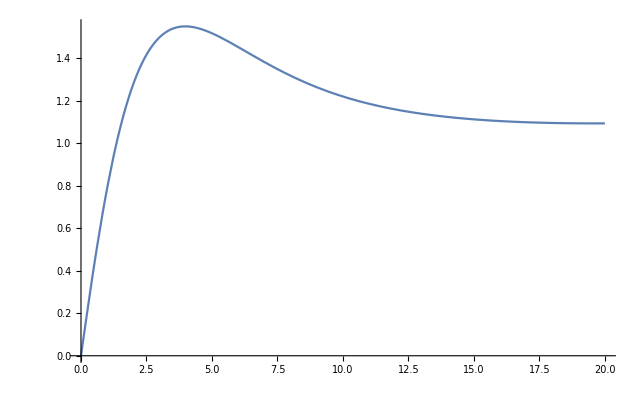

```mathematica
Plot[inter[x/0.197],{x,0,20},PlotRange->All]
```

```mathematica
check=Interpolation[ToExpression[Import["vel_pot/ReVsu50.dat"]]]
```

InterpolatingFunction[{{0., 100.}}, <>]

```mathematica
ϵImp[r_,u_,mD_,T_]:=Re[1/(2π)T NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))mD^2/(Πpar[x,u,mD]-Conjugate[Πpar[x,u,mD]])1/r Cos[x] (2 √Conjugate[Πpar[x,u,mD]] (CoshIntegral[r √Conjugate[Πpar[x,u,mD]] Cos[x]] Sinh[r √Conjugate[Πpar[x,u,mD]] Cos[x]]-Cosh[r √Conjugate[Πpar[x,u,mD]] Cos[x]] SinhIntegral[r √Conjugate[Πpar[x,u,mD]] Cos[x]])+r Conjugate[Πpar[x,u,mD]] Cos[x] (Cosh[r √Conjugate[Πpar[x,u,mD]] Cos[x]] CoshIntegral[r √Conjugate[Πpar[x,u,mD]] Cos[x]]-Sinh[r √Conjugate[Πpar[x,u,mD]] Cos[x]] SinhIntegral[r √Conjugate[Πpar[x,u,mD]] Cos[x]])+√Πpar[x,u,mD] (-CoshIntegral[r Cos[x] √Πpar[x,u,mD]] (r Cos[x] Cosh[r Cos[x] √Πpar[x,u,mD]] √Πpar[x,u,mD]+2 Sinh[r Cos[x] √Πpar[x,u,mD]])+(2 Cosh[r Cos[x] √Πpar[x,u,mD]]+r Cos[x] √Πpar[x,u,mD] Sinh[r Cos[x] √Πpar[x,u,mD]]) SinhIntegral[r Cos[x] √Πpar[x,u,mD]])),{x,0,π/2},WorkingPrecision->20]];
```

```mathematica
ImVsTab[u1_,mD1_,σ1_,T1_]:=Block[{u=u1,mD=mD1,σ=σ1,T=T1,tab0,tab1,inter0,inter1,inter2,temp,tab2},tab0=ParallelTable[{r,-4π σ r^2 ϵImp[r,u,mD,T]},{r,10^-10,20,1/100}];
inter0=Interpolation[tab0];
inter1[r_]:=NIntegrate[inter0[r1],{r1,0,r}];
temp=inter1[0];
tab1=ParallelTable[{r,inter1[r]-temp},{r,10^-10,20,1/100}];
inter1=Interpolation[tab1];
inter2[r_]:=NIntegrate[inter1[r1],{r1,0,r}];
tab2=ParallelTable[{r,inter2[r]},{r,0,20,1/100}];
Export["vel_pot/ImVsu"<>Round[100 u]<>".dat",tab2];
Return[Interpolation[tab2]]];
```

```mathematica
inter=ImVsTab[1/2,2/10,17/100,155/1000]
```

```mathematica
Plot[inter[x/0.197],{x,0,1.5},PlotRange->All]
```

### Combined

```mathematica
ReVcp[r_,mD_,u_,α_]:=-α/r+α NIntegrate[Sin[θ] √Re[Πpar[θ,u,mD]] Exp[-√Re[Πpar[θ,u,mD]]r Cos[θ]],{θ,0,π/2}];
```

```mathematica
ReVs=ReVsTab[1/2,2/10,17/100];
```

```mathematica
ImVcp[r_,mD_,u_,α_,T_]:=2 α T NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))mD^2/(Πpar[x,u,mD]-Conjugate[Πpar[x,u,mD]])(Sinh[√Πpar[x,u,mD] r Cos[x]]SinhIntegral[√Πpar[x,u,mD] r Cos[x]]-Cosh[√Πpar[x,u,mD] r Cos[x]]CoshIntegral[√Πpar[x,u,mD] r Cos[x]]-Sinh[√Conjugate[Πpar[x,u,mD]] r Cos[x]]SinhIntegral[√Conjugate[Πpar[x,u,mD]] r Cos[x]]+Cosh[√Conjugate[Πpar[x,u,mD]] r Cos[x]]CoshIntegral[√Conjugate[Πpar[x,u,mD]] r Cos[x]]),{x,0,π/2}];
```

```mathematica
ImVs=ImVsTab[1/2,2/10,17/100,155/1000];
```

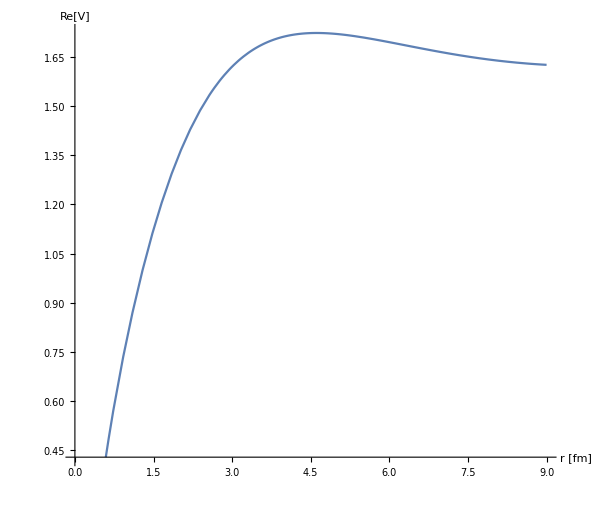

```mathematica
Plot[ReVcp[r/0.197,2/10,1/2,1/2]+ReVs[r/0.197],{r,1/100,9},Filling->None,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600},Axes->True]
```

```mathematica
ImVcp[10^-10,2/10,1/2,1/2,155/1000]
```

0.081463

```mathematica
ImVcp[5/0.197,2/10,1/2,1/2,155/1000]
```

-0.00576221+4.93151×10^-17 ⅈ

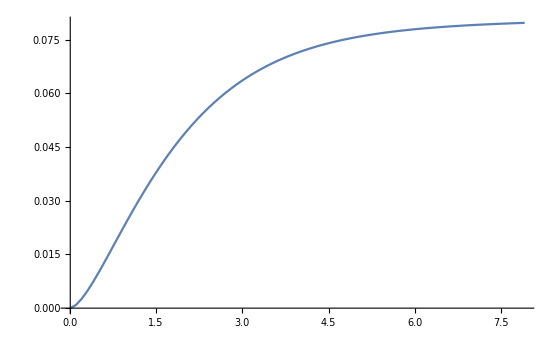

```mathematica
DiscretePlot[Re[ImVcp[r/0.197,2/10,1/2,1/2,155/1000]]-ImVcp[10^-10,2/10,1/2,1/2,155/1000],{r,1/100,8,1/10},Filling->None,Joined->True,PlotRange->All]
```

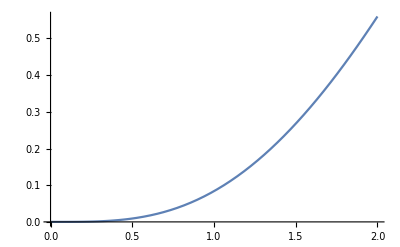

```mathematica
Plot[-ImVs[r/0.197],{r,0,2}]
```

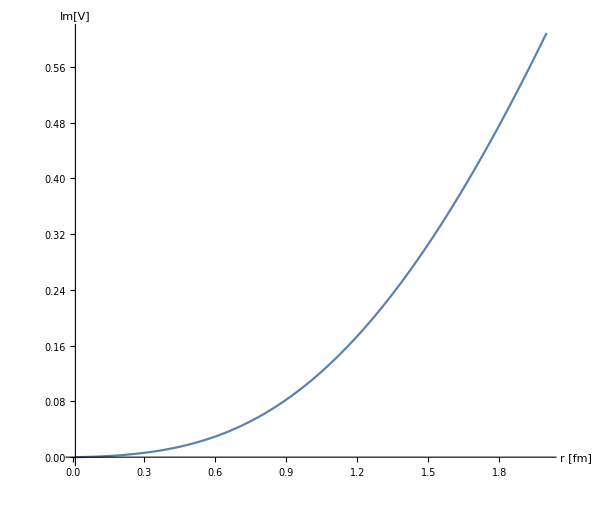

```mathematica
DiscretePlot[Re[ImVcp[r/0.197,2/10,1/2,1/2,155/1000]]-ImVs[r/0.197]-Re[ImVcp[10^-10,2/10,1/2,1/2,155/1000]],{r,1/100,2,1/100},Filling->None,Joined->True,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},ImageSize->{600,600},Axes->True]
```